```mathematica
MatrixForm[Table[LegendreP[l,Cos[θ]],{l,0,7}]]
```

```mathematica
MatrixForm[TrigReduce[({{1}, {Cos[θ]}, {1/2 (-1+3 Cos[θ]^2)}, {1/2 (-3 Cos[θ]+5 Cos[θ]^3)}, {1/8 (3-30 Cos[θ]^2+35 Cos[θ]^4)}, {1/8 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)}, {1/16 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)}, {1/16 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)}})]]
```

(1
Cos[θ]
1/4 (1+3 Cos[2 θ])
1/8 (3 Cos[θ]+5 Cos[3 θ])
1/64 (9+20 Cos[2 θ]+35 Cos[4 θ])
1/128 (30 Cos[θ]+35 Cos[3 θ]+63 Cos[5 θ])
1/512 (50+105 Cos[2 θ]+126 Cos[4 θ]+231 Cos[6 θ])
(175 Cos[θ]+189 Cos[3 θ]+231 Cos[5 θ]+429 Cos[7 θ])/1024)

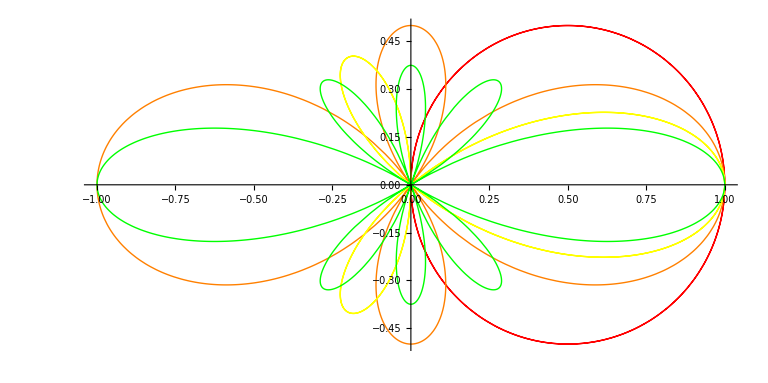

```mathematica
PolarPlot[{Cos[θ],1/4 (1+3 Cos[2 θ]),1/8 (3 Cos[θ]+5 Cos[3 θ]),1/64 (9+20 Cos[2 θ]+35 Cos[4 θ])},{θ,0,2π},PlotStyle->{Red,Orange,Yellow,Green}]
```

```mathematica
MatrixForm[Re[TrigReduce[Table[SphericalHarmonicY[l,m,θ,ϕ],{l,0,7},{m,0,7}]]]]
```

(1/(2 √π) | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/2 √(3/π) Re[Cos[θ]] | -1/2 √(3/(2 π)) Re[ⅇ^(ⅈ ϕ) Sin[θ]] | 0 | 0 | 0 | 0 | 0 | 0
1/8 (√(5/π)+3 √(5/π) Re[Cos[2 θ]]) | -1/4 √(15/(2 π)) Re[ⅇ^(ⅈ ϕ) Sin[2 θ]] | -1/8 √(15/(2 π)) Re[ⅇ^(2 ⅈ ϕ) (-1+Cos[2 θ])] | 0 | 0 | 0 | 0 | 0
1/16 Re[3 √(7/π) Cos[θ]+5 √(7/π) Cos[3 θ]] | -1/32 √(21/π) Re[ⅇ^(ⅈ ϕ) (Sin[θ]+5 Sin[3 θ])] | 1/16 √(105/(2 π)) Re[ⅇ^(2 ⅈ ϕ) (Cos[θ]-Cos[3 θ])] | -1/32 √(35/π) Re[ⅇ^(3 ⅈ ϕ) (3 Sin[θ]-Sin[3 θ])] | 0 | 0 | 0 | 0
(3 (9+Re[20 Cos[2 θ]+35 Cos[4 θ]]))/(128 √π) | -3/64 √(5/π) Re[ⅇ^(ⅈ ϕ) (2 Sin[2 θ]+7 Sin[4 θ])] | 3/64 √(5/(2 π)) Re[ⅇ^(2 ⅈ ϕ) (3+4 Cos[2 θ]-7 Cos[4 θ])] | -3/64 √(35/π) Re[ⅇ^(3 ⅈ ϕ) (2 Sin[2 θ]-Sin[4 θ])] | -3/128 √(35/(2 π)) Re[ⅇ^(4 ⅈ ϕ) (-3+4 Cos[2 θ]-Cos[4 θ])] | 0 | 0 | 0
1/256 Re[30 √(11/π) Cos[θ]+35 √(11/π) Cos[3 θ]+63 √(11/π) Cos[5 θ]] | -1/256 √(165/(2 π)) Re[ⅇ^(ⅈ ϕ) (2 Sin[θ]+7 Sin[3 θ]+21 Sin[5 θ])] | 1/128 √(1155/(2 π)) Re[ⅇ^(2 ⅈ ϕ) (2 Cos[θ]+Cos[3 θ]-3 Cos[5 θ])] | -1/512 √(385/π) Re[ⅇ^(3 ⅈ ϕ) (6 Sin[θ]+13 Sin[3 θ]-9 Sin[5 θ])] | 3/256 √(385/(2 π)) Re[ⅇ^(4 ⅈ ϕ) (2 Cos[θ]-3 Cos[3 θ]+Cos[5 θ])] | -3/512 √(77/π) Re[ⅇ^(5 ⅈ ϕ) (10 Sin[θ]-5 Sin[3 θ]+Sin[5 θ])] | 0 | 0
(50 √(13/π)+Re[105 √(13/π) Cos[2 θ]+126 √(13/π) Cos[4 θ]+231 √(13/π) Cos[6 θ]])/1024 | -1/512 √(273/(2 π)) Re[ⅇ^(ⅈ ϕ) (5 Sin[2 θ]+12 Sin[4 θ]+33 Sin[6 θ])] | (√(1365/π) Re[ⅇ^(2 ⅈ ϕ) (10+17 Cos[2 θ]+6 Cos[4 θ]-33 Cos[6 θ])])/2048 | -(√(1365/π) Re[ⅇ^(3 ⅈ ϕ) (9 Sin[2 θ]+12 Sin[4 θ]-11 Sin[6 θ])])/1024 | (3 √(91/(2 π)) Re[ⅇ^(4 ⅈ ϕ) (10+5 Cos[2 θ]-26 Cos[4 θ]+11 Cos[6 θ])])/1024 | -(3 √(1001/π) Re[ⅇ^(5 ⅈ ϕ) (5 Sin[2 θ]-4 Sin[4 θ]+Sin[6 θ])])/1024 | -(√(3003/π) Re[ⅇ^(6 ⅈ ϕ) (-10+15 Cos[2 θ]-6 Cos[4 θ]+Cos[6 θ])])/2048 | 0
Re[175 √(15/π) Cos[θ]+189 √(15/π) Cos[3 θ]+231 √(15/π) Cos[5 θ]+429 √(15/π) Cos[7 θ]]/2048 | -(√(105/(2 π)) Re[ⅇ^(ⅈ ϕ) (25 Sin[θ]+81 Sin[3 θ]+165 Sin[5 θ]+429 Sin[7 θ])])/4096 | (3 √(35/π) Re[ⅇ^(2 ⅈ ϕ) (75 Cos[θ]+57 Cos[3 θ]+11 Cos[5 θ]-143 Cos[7 θ])])/4096 | -(3 √(35/(2 π)) Re[ⅇ^(3 ⅈ ϕ) (45 Sin[θ]+117 Sin[3 θ]+121 Sin[5 θ]-143 Sin[7 θ])])/4096 | (3 √(385/(2 π)) Re[ⅇ^(4 ⅈ ϕ) (15 Cos[θ]-3 Cos[3 θ]-25 Cos[5 θ]+13 Cos[7 θ])])/2048 | -(3 √(385/(2 π)) Re[ⅇ^(5 ⅈ ϕ) (25 Sin[θ]+33 Sin[3 θ]-43 Sin[5 θ]+13 Sin[7 θ])])/4096 | (3 √(5005/π) Re[ⅇ^(6 ⅈ ϕ) (5 Cos[θ]-9 Cos[3 θ]+5 Cos[5 θ]-Cos[7 θ])])/4096 | -(3 √(715/(2 π)) Re[ⅇ^(7 ⅈ ϕ) (35 Sin[θ]-21 Sin[3 θ]+7 Sin[5 θ]-Sin[7 θ])])/4096)

```mathematica
SphericalPlot3D[(3 √(385/(2 π)) Re[ⅇ^(4 ⅈ ϕ) (15 Cos[θ]-3 Cos[3 θ]-25 Cos[5 θ]+13 Cos[7 θ])])/2048,{θ,0,Pi},{ϕ,0,2Pi}]
```

-Graphics3D-